# VdP cuántico forzado: Fock, FLS y representación de fase

Igual que vdp_sin_forzamiento.nb, con un forzamiento ℰ cos(Ωt)(a + a†). Ganancia de un fonón (κp) y pérdida de dos (κm), con el convenio de las notas: ℏ = 1 y disipador D[L]ρ = LρL† − (L†Lρ + ρL†L)/2. Ojo: en Mathematica E es el número e, así que la amplitud se escribe ℰ.

Todo está en el marco que gira con el forzamiento: H = Δ a†a + (ℰ/2)(a + a†), con Δ = ω − Ω y la aproximación de onda rotante. En el sistema de laboratorio H depende del tiempo y no hay estado estacionario (es periódico), así que no se puede usar aquí. Los disipadores no cambian al girar.

## 0. Cargar el paquete

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "RepresentacionFase.wl"}]]
```

```mathematica
$Assumptions = κp > 0 && κm > 0 && ℰ > 0 && Δ ∈ Reals;
```

## 1. Lo que se elige: niveles, hamiltoniano y saltos

Igual que en el cuaderno sin forzamiento. Con d ≥ 4 la solución simbólica crece mucho: conviene dar valores numéricos a los parámetros antes de llamar a estadoEstacionario.

```mathematica
d = 3;
H = Δ ad ** a + ℰ/2 (a + ad);
saltos = {{κp, +1}, {κm, -2}};
```

```mathematica
MatrixForm[matrizFock[H, d]]
```

(0 | ℰ/2 | 0
ℰ/2 | Δ | ℰ/(√2)
0 | ℰ/(√2) | 2 Δ)

## 2. Ecuación de Lindblad en el espacio de Fock–Liouville

```mathematica
ℒ = liouvilliano[H, saltos, d];
```

Ordenada por bloques k = n − m (k = 0, 1, 2, −1, −2). Ahora el forzamiento conecta cada bloque k con k ± 1, así que ℒ ya no es diagonal por bloques: es la ruptura de la simetría de fase.

```mathematica
o = ordenPorK[d];
TableForm[ℒ[[o, o]], TableHeadings -> {etiquetasFLS[d][[o]], etiquetasFLS[d][[o]]}]
```

| ρ00 | ρ11 | ρ22 | ρ10 | ρ21 | ρ20 | ρ01 | ρ12 | ρ02
ρ00 | -κp | 0 | 2 κm | -(ⅈ ℰ)/2 | 0 | 0 | (ⅈ ℰ)/2 | 0 | 0
ρ11 | κp | -2 κp | 0 | (ⅈ ℰ)/2 | -(ⅈ ℰ)/(√2) | 0 | -(ⅈ ℰ)/2 | (ⅈ ℰ)/(√2) | 0
ρ22 | 0 | 2 κp | -2 κm | 0 | (ⅈ ℰ)/(√2) | 0 | 0 | -(ⅈ ℰ)/(√2) | 0
ρ10 | -(ⅈ ℰ)/2 | (ⅈ ℰ)/2 | 0 | -ⅈ Δ-(3 κp)/2 | 0 | -(ⅈ ℰ)/(√2) | 0 | 0 | 0
ρ21 | 0 | -(ⅈ ℰ)/(√2) | (ⅈ ℰ)/(√2) | √2 κp | -ⅈ Δ-κm-κp | (ⅈ ℰ)/2 | 0 | 0 | 0
ρ20 | 0 | 0 | 0 | -(ⅈ ℰ)/(√2) | (ⅈ ℰ)/2 | -2 ⅈ Δ-κm-κp/2 | 0 | 0 | 0
ρ01 | (ⅈ ℰ)/2 | -(ⅈ ℰ)/2 | 0 | 0 | 0 | 0 | ⅈ Δ-(3 κp)/2 | 0 | (ⅈ ℰ)/(√2)
ρ12 | 0 | (ⅈ ℰ)/(√2) | -(ⅈ ℰ)/(√2) | 0 | 0 | 0 | √2 κp | ⅈ Δ-κm-κp | -(ⅈ ℰ)/2
ρ02 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ ℰ)/(√2) | -(ⅈ ℰ)/2 | 2 ⅈ Δ-κm-κp/2

Conservación de la traza: vec(𝟙)·ℒ = 0, así que det ℒ = 0.

```mathematica
Simplify[vecFLS[IdentityMatrix[d]] . ℒ]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
Simplify[Det[ℒ]]
```

0

## 3. Estado estacionario

Con κm finito la solución exacta de 3 niveles es una expresión larga (tarda unos segundos y no la muestro). Se comprueba que es estacionaria y se toma el límite cuántico.

```mathematica
ρss = Simplify[estadoEstacionario[ℒ, d]];
LeafCount[ρss]
```

4202

```mathematica
Simplify[ℒ . vecFLS[ρss]]  (* tiene que dar todo ceros *)
```

{0,0,0,0,0,0,0,0,0}

Límite cuántico, κm → ∞:

```mathematica
ρlim = Simplify[Limit[ρss, κm -> Infinity, Assumptions -> κp > 0 && ℰ > 0 && Δ ∈ Reals]];
MatrixForm[ρlim]
```

((3 ℰ^2+8 Δ^2+18 κp^2)/(6 ℰ^2+12 Δ^2+27 κp^2) | (ℰ (-2 Δ+3 ⅈ κp))/(3 (2 ℰ^2+4 Δ^2+9 κp^2)) | 0
-(ℰ (2 Δ+3 ⅈ κp))/(3 (2 ℰ^2+4 Δ^2+9 κp^2)) | (3 ℰ^2+4 Δ^2+9 κp^2)/(6 ℰ^2+12 Δ^2+27 κp^2) | 0
0 | 0 | 0)

En el marco rotante ⟨a⟩ = Tr(aρ) = ρ10. En el laboratorio ⟨a⟩(t) = ρ10 e^{−iΩt}: el oscilador oscila a la frecuencia del forzamiento, no a ω.

```mathematica
Simplify[Tr[matrizFock[a, d] . ρlim]]
```

-(ℰ (2 Δ+3 ⅈ κp))/(3 (2 ℰ^2+4 Δ^2+9 κp^2))

## 4. Representación de fase

Diccionario de las notas (ecs. 41–42), con Dθ = i∂θ y Dθp = −i∂θp: aρ → e^{iθ}√Dθ K, a†ρ → e^{−iθ}√(Dθ+1) K, ρa → e^{iθp}√(Dθp+1) K, ρa† → e^{−iθp}√Dθp K. Ejemplo con ρ = |2⟩⟨1|:

```mathematica
K21 = nucleo[{{0, 0, 0}, {0, 0, 0}, {0, 1, 0}}];
TableForm[{{"aρ", accionIzq[a, K21]}, {"a†ρ", accionIzq[ad, K21]}, {"ρa", accionDer[a, K21]}, {"ρa†", accionDer[ad, K21]}}]
```

aρ | √2 ⅇ^(-ⅈ θ+ⅈ θp)
a†ρ | √3 ⅇ^(-3 ⅈ θ+ⅈ θp)
ρa | √2 ⅇ^(-2 ⅈ θ+2 ⅈ θp)
ρa† | ⅇ^(-2 ⅈ θ)

Núcleo y distribución de fase en el límite cuántico. Ahora K tiene los términos e^{−iθ} y e^{iθp} sueltos (los de ρ10 y ρ01), y por eso P(θ) deja de ser plana:

```mathematica
K = Simplify[nucleo[ρlim]]
```

(ⅇ^(-ⅈ θ) (ⅇ^(ⅈ (θ+θp)) ℰ (-2 Δ+3 ⅈ κp)-ℰ (2 Δ+3 ⅈ κp)+ⅇ^(ⅈ θp) (3 ℰ^2+4 Δ^2+9 κp^2)+ⅇ^(ⅈ θ) (3 ℰ^2+8 Δ^2+18 κp^2)))/(3 (2 ℰ^2+4 Δ^2+9 κp^2))

```mathematica
P = distribucionFase[ρlim]
```

(6 ℰ^2+12 Δ^2+27 κp^2-4 ℰ Δ Cos[θ]-6 ℰ κp Sin[θ])/(12 π ℰ^2+24 π Δ^2+54 π κp^2)

Comprobaciones del diccionario: la ecuación de Lindblad en fase (con el término del forzamiento) coincide con la de Fock, y el núcleo estacionario exacto de 3 niveles cumple ∂t K = 0. Para esto último hay que usar ρss (con κm finito): ρlim solo es el orden dominante. Tarda unos segundos.

```mathematica
comprobarDiccionario[H, saltos, d]
```

True

```mathematica
Simplify[matrizDeNucleo[lindbladFase[nucleo[ρss], H, saltos, d], d]]
```

{{0,0,0},{0,0,0},{0,0,0}}

## 5. Distribución de fase

Δ = ω − Ω es un parámetro: lo fija quien pone el forzamiento. Primero, en resonancia (Δ = 0) y con varias amplitudes, en el límite cuántico. El pico está en θ = 3π/2, la fase que da Lee para Δ = 0.

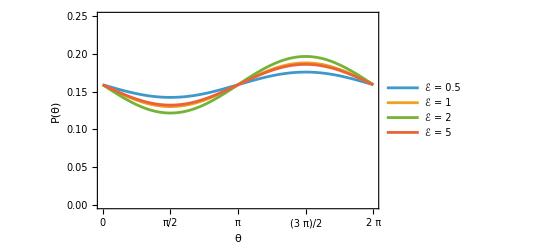

```mathematica
Plot[Evaluate[Table[P /. {κp -> 1, Δ -> 0, ℰ -> x}, {x, {0.5, 1, 2, 5}}]], {θ, 0, 2 Pi},
 PlotRange -> {0, 0.25}, Frame -> True, FrameLabel -> {"θ", "P(θ)"},
 FrameTicks -> {{Automatic, None}, {Range[0, 2 Pi, Pi/2], None}}, GridLines -> {{3 Pi/2}, {1/(2 Pi)}},
 PlotLegends -> {"ℰ = 0.5", "ℰ = 1", "ℰ = 2", "ℰ = 5"}]
```

Ahora con amplitud fija y varios desintonizados. Al crecer |Δ|, el pico baja y se desplaza: la fase de anclaje deja de ser 3π/2, igual que en Adler, donde sin ψ* = ν/ϵ.

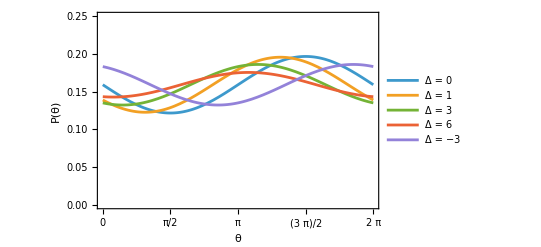

```mathematica
Plot[Evaluate[Table[P /. {κp -> 1, Δ -> x, ℰ -> 2}, {x, {0, 1, 3, 6, -3}}]], {θ, 0, 2 Pi},
 PlotRange -> {0, 0.25}, Frame -> True, FrameLabel -> {"θ", "P(θ)"},
 FrameTicks -> {{Automatic, None}, {Range[0, 2 Pi, Pi/2], None}}, GridLines -> {{3 Pi/2}, {1/(2 Pi)}},
 PlotLegends -> {"Δ = 0", "Δ = 1", "Δ = 3", "Δ = 6", "Δ = −3"}]
```

¿Cuánto se aleja el límite del caso de 3 niveles con κm finito? Con κm = 20κp, el valor de Lee para el régimen cuántico:

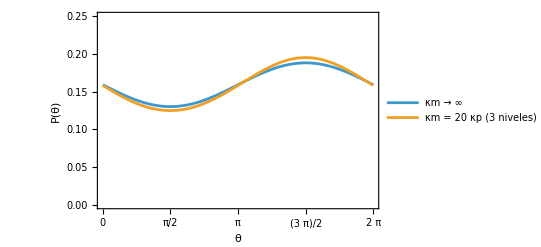

```mathematica
Pfin = distribucionFase[ρss /. {κp -> 1, κm -> 20, Δ -> 0, ℰ -> 1}];
Plot[{P /. {κp -> 1, Δ -> 0, ℰ -> 1}, Pfin}, {θ, 0, 2 Pi},
 PlotRange -> {0, 0.25}, Frame -> True, FrameLabel -> {"θ", "P(θ)"},
 FrameTicks -> {{Automatic, None}, {Range[0, 2 Pi, Pi/2], None}},
 PlotLegends -> {"κm → ∞", "κm = 20 κp (3 niveles)"}]
```

Para explorar a mano (unidades de κp):

```mathematica
Manipulate[
 Plot[P /. {κp -> 1, Δ -> det, ℰ -> amp}, {θ, 0, 2 Pi}, PlotRange -> {0, 0.25},
  Frame -> True, FrameLabel -> {"θ", "P(θ)"}, FrameTicks -> {{Automatic, None}, {Range[0, 2 Pi, Pi/2], None}}],
 {{det, 0, "Δ/κp"}, -10, 10}, {{amp, 1, "ℰ/κp"}, 0, 15}]
```

## 6. Lengua de Arnold

P(θ) = [1 + 2|ρ10| cos(θ − arg ρ10)]/2π, así que |ρ10| mide cuánto se sincroniza el oscilador con el forzamiento. Mapa de |ρ10| en el plano (Δ, ℰ), en el límite cuántico y en unidades de κp. Compáralo con la lengua de Adler del paso 2: ¿dónde está el máximo para cada Δ, y cuánto vale?

```mathematica
modρ10 = Simplify[ComplexExpand[Abs[ρlim[[2, 1]]]]]
```

(ℰ √(4 Δ^2+9 κp^2))/(6 ℰ^2+12 Δ^2+27 κp^2)

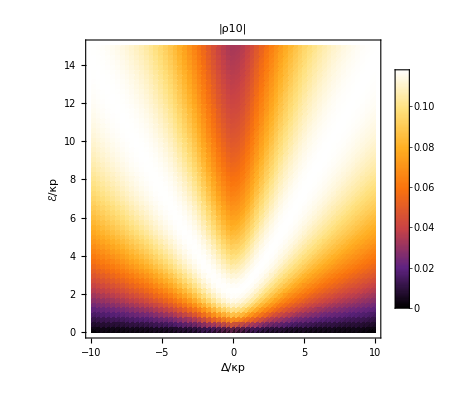

```mathematica
DensityPlot[modρ10 /. κp -> 1, {Δ, -10, 10}, {ℰ, 0, 15},
 PlotPoints -> 60, ColorFunction -> "SunsetColors", PlotLegends -> Automatic,
 FrameLabel -> {"Δ/κp", "ℰ/κp"}, PlotLabel -> "|ρ10|"]
```

## 7. El núcleo de fase K(θ, θp)

K es complejo y depende de dos ángulos, así que se dibujan su módulo y su fase en el cuadrado [0, 2π]×[0, 2π]. La diagonal θ = θp (línea discontinua) es 2πP(θ). Lo que se aleja de la diagonal son las coherencias entre fases distintas: dependen de φ = θ − θp y guardan las poblaciones. Izquierda, sin forzamiento (ℰ = 0): K solo depende de θ − θp y salen bandas paralelas a la diagonal. Derecha, con forzamiento: los términos e^{−iθ} y e^{iθp} rompen esa simetría.

```mathematica
Kn[amp_, det_] := K /. {κp -> 1, Δ -> det, ℰ -> amp};
ticks = {{Range[0, 2 Pi, Pi/2], None}, {Range[0, 2 Pi, Pi/2], None}};
panelK[f_, rango_, colores_, etiqueta_, amp_, det_] := DensityPlot[f[Kn[amp, det]], {θ, 0, 2 Pi}, {θp, 0, 2 Pi},
  PlotPoints -> 40, PlotRange -> rango, ColorFunction -> colores, ColorFunctionScaling -> False,
  PlotLegends -> Automatic, FrameLabel -> {"θ", "θp"}, FrameTicks -> ticks, PlotLabel -> etiqueta,
  Epilog -> {White, Dashed, Line[{{0, 0}, {2 Pi, 2 Pi}}]}, ImageSize -> 280];
```

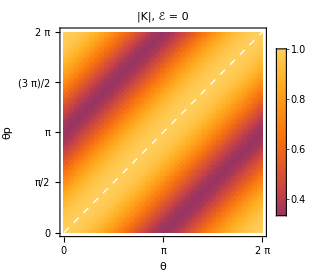
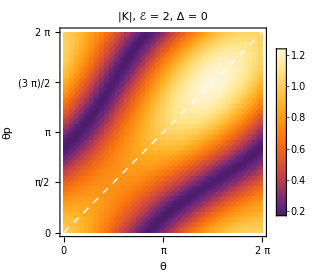
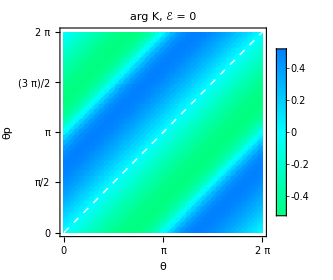
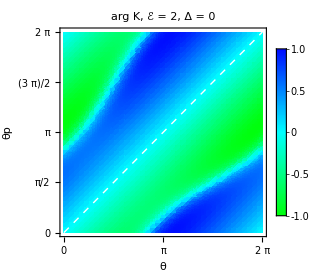
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
modulo = ColorData[{"SunsetColors", {0, 1.3}}];
fase = (Hue[(# + Pi)/(2 Pi)] &);
Grid[{
  {panelK[Abs, {0, 1.3}, modulo, "|K|, ℰ = 0", 0, 0], panelK[Abs, {0, 1.3}, modulo, "|K|, ℰ = 2, Δ = 0", 2, 0]},
  {panelK[Arg, {-Pi, Pi}, fase, "arg K, ℰ = 0", 0, 0], panelK[Arg, {-Pi, Pi}, fase, "arg K, ℰ = 2, Δ = 0", 2, 0]}}]
```

Para explorar (unidades de κp):

```mathematica
Manipulate[panelK[Abs, {0, 1.3}, modulo, "|K|", amp, det],
 {{det, 0, "Δ/κp"}, -10, 10}, {{amp, 2, "ℰ/κp"}, 0, 15}]
```